```mathematica
searchlink = "https://en.wikipedia.org/w/index.php?title=Special:Search&limit=500&offset=0&profile=default&search=computational&searchToken=b9fbzhit5sdhvvts5aa00u74l";
xmlResults = Import[searchlink, "XMLObject"];
articles = Union[Flatten[Cases[xmlResults,XMLElement[_,{_,_,
	"title"->str_String/;
		((StringMatchQ[str,StartOfString~~"Computational"~~__])&&!(StringContainsQ[str,"Journal",IgnoreCase->True])),_},_]->{str},Infinity]]];
```

```mathematica
TitleToInfo[articleTitle_String]:=
	AssociationMap[WikipediaData[articleTitle, #]&,
		{"ArticlePlaintext", "ExternalLinks", "ArticleContributors", "PageID", "SummaryPlaintext", "LanguagesList", "LinksList", "BacklinksList"}];
```

```mathematica
compData = AssociationMap[TitleToInfo, articles];
```

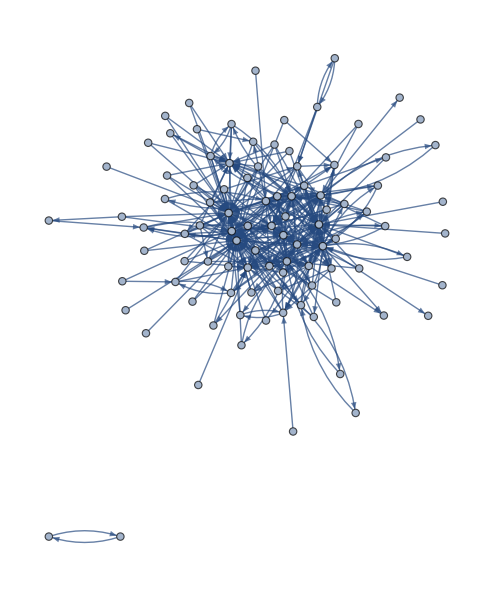

```mathematica
edgeSet = Flatten@Map[Thread, Normal@compData[[;;, "LinksList"]]];
theGraph = Graph[edgeSet];
verticesToKeep = Union[Keys@Select[AssociationThread[VertexList[theGraph], VertexInDegree[theGraph]], # ≥ 20 &], Keys@compData];
filteredEdges = Select[Normal@edgeSet, And[MemberQ[verticesToKeep, #[[1]]], MemberQ[verticesToKeep, #[[2]]]] &];
Graph[filteredEdges, VertexLabels-> Placed[Automatic, Tooltip]]
```

```mathematica
CommunityGraphPlot[filteredEdges,VertexLabels->Placed[Automatic,Tooltip],Method->"Hierarchical"]
```

-Graphics-

```mathematica
AssociationThread[VertexList[theGraph], VertexOutDegree[theGraph]]
```

<|Computational aeroacoustics→14,Acoustic analogy→0,Acoustic theory→0,Aeroacoustics→0,Boundary element method→0,Computational Aeroacoustics→0,Computational fluid dynamics→177,Gustav Kirchhoff→0,Hermann von Helmholtz→0,John Ffowcs Williams→0,Mach number→0,Navier-Stokes equation→0,Noise→0,4601,Trust metric→0,Virtual community→0,Computational visualistics→18,Art history→0,Data type→0,Image→0,Information visualization→0,Mandelbrot set→0,Otto-von-Guericke University Magdeburg→0,Perception→0,University of Koblenz and Landau→0,Computational X→10,Geoffrey C. Fox→0|>
 |  |  |  |

```mathematica
DumpSave["/Users/ethan/Desktop/WSS2017/saved_data/compData.mx", compData];
```

```mathematica
compOnlyEdges =Flatten@Map[Thread,Table[Map[Thread,articles[[i]]-> Intersection[Keys[compData],compData[[i]][["LinksList"]]]],{i,1,100}]];
```

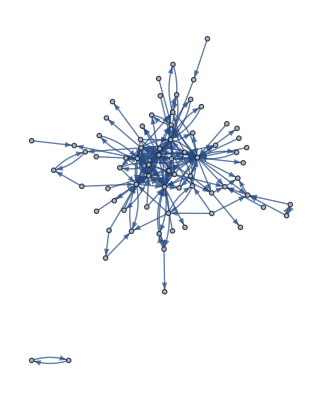

```mathematica
Graph[compOnlyEdges,VertexLabels->Placed[Automatic,Tooltip]]
```

```mathematica
CommunityGraphPlot[compOnlyEdges,VertexLabels->Placed[Automatic,Tooltip],Method->"Hierarchical"]
```

-Graphics-